#### Hard Ham Graphs

From Science Nature Computer Science (2022) 3:372 , Sleegers & van den Berg

These graphs, which have no Ham cycles, are “tough” in the sense as measured by different backtracking programs. (On the other hand, as drawn, there is a simple proof they don’t have ham cycs!) The authors found these by evolutionary algorithms,

```mathematica
hardgraphDirected=Graph@(Join@@Join[Table[DirectedEdge[k,#]&/@Drop[Range[2#+1],{k}],{k,#}],
Table[DirectedEdge[k,#]&/@Range[#],{k,#+1,2#+1}]
])&
```

```mathematica
hardgraphA=Graph@(Join@@Table[UndirectedEdge[k,#]&/@Range[k+1,2#+1],{k,#}])&
```

Graph[Join@@Table[(k<->#1&)/@Range[k+1,2 #1+1],{k,#1}]]&

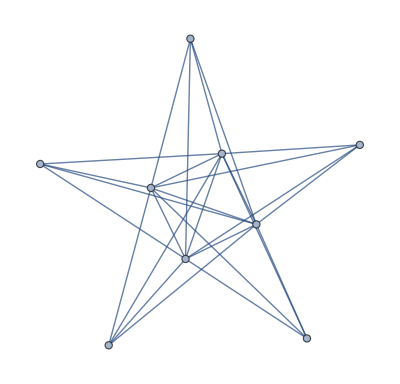

```mathematica
hardgraphA@4
```

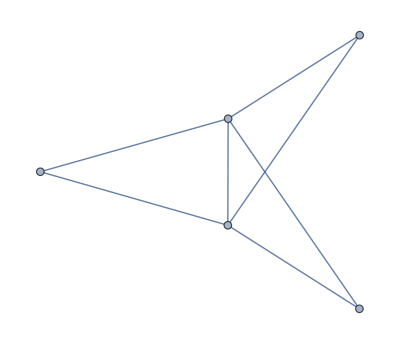
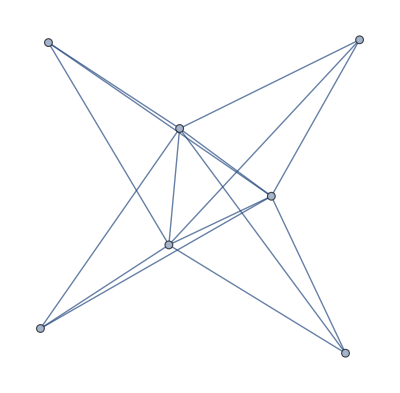
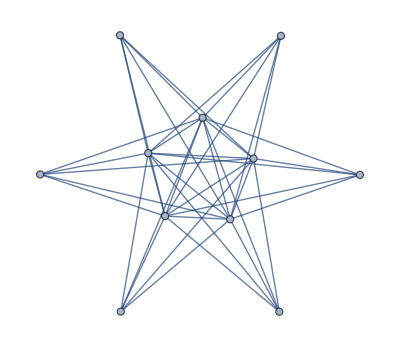
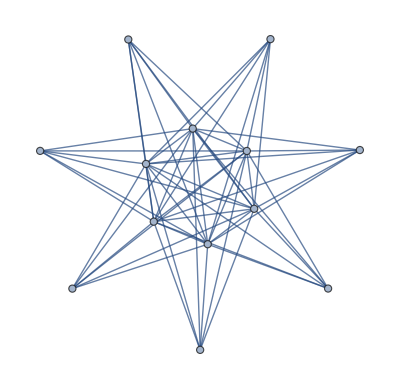
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[hardgraphA@k,{k,2,6}]
```

On the other hand, these are the ‘hardest’ to find that do have ham cycles. The paper reports that these are

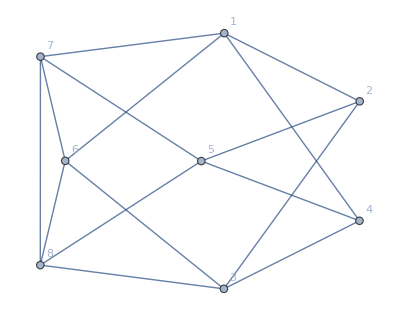

```mathematica
Graph[#,VertexLabels->"Name"]&@(Join@@((a=#[[1]];UndirectedEdge[a,#]&/@#[[2]])&/@{{1,{2,4,6,7}},{2,{3,5}},{3,{4,6,8}},{4,{5}},{5,{7,8}},{6,{7,8}},{7,{8}}}))
```